# Buchberger Gröbner Basis Algorithm

### Code

```mathematica
LT[p_?PolynomialQ,vars_,or_]:=First[MonomialList[p,vars,or]]
```

```mathematica
lc[f_,g_,vars_List,or_]:=With[{w=PolynomialLCM[LT[f,vars,or],LT[g,vars,or]]},w/(w/.Thread[vars->1])]
```

```mathematica
S[f_,g_,vars_List,or_]:=(f lc[LT[f,vars,or],LT[g,vars,or],vars,or])/LT[f,vars,or]-(g lc[LT[f,vars,or],LT[g,vars,or],vars,or])/LT[g,vars,or]
```

```mathematica
LP[{i_,j_}]:=If[i<j, {i,j},{j,i}]
```

```mathematica
Crit[{i_,j_},vars_,G_,B_,ord_]:=Module[{q,r},
For[l=1,l≤ Length[G],l++,
If[MemberQ[B,LP[{i,l}]] || MemberQ[B,LP[{j,l}]] || MemberQ[{i,j},l],
Nothing,
{q,r}=PolynomialReduce[lc[Part[G,i],Part[G,j],vars,ord],LT[Part[G,l],vars,ord], vars, MonomialOrder-> ord];
If[r==0, Return[True];Break[];, Nothing];
];
];
Return[False];
]
```

```mathematica
MonomialReduce[F_,ord_]:=Module[{i,j,q,r,k,B,G,K,R,pos,vars},
vars=Variables[F];
K=CoefReduce[F,ord];
G={};

For[i=1,i≤ Length[K],i++,
G=AppendTo[G,LT[Part[K,i],vars,ord]];
];
R={};
B=G;

For[j=1,j≤ Length[B],j++,
k=Part[B,j];
pos=Position[G,k];

{q,r}=PolynomialReduce[k,Delete[G,First[pos]],vars,MonomialOrder-> ord];
If[r==0,
G=Delete[G,First[pos]];
R=AppendTo[R,{j}],
Nothing];
];

G=Delete[K,R];
Return[G];
]
```

```mathematica
ImpGrob[F_,ord_]:=Module[{s,t,p,i,j,q,r,a,b,k,vars,G,B},
s=Length[F];
B={};
vars=Variables[F];

For[a=1,a≤ s-1,a++, Do[AppendTo[B,{a,b}],{b,a+1,s}]];
G=F;
t=s;

While[Length[B]≠ 0,
p=Part[B,1];
i=Part[p,1];
j=Part[p,2];

If[FullSimplify[lc[Part[G,i],Part[G,j],vars,ord]=!=LT[Part[G,i],vars,ord]*LT[Part[G,j],vars,ord]] && Crit[{i,j},vars,G,B,ord]==False,
{q,r}=PolynomialReduce[S[Part[G,i],Part[G,j],vars,ord],G,vars,MonomialOrder-> ord];
If[r=!=0,
t=t+1;
AppendTo[G,r];
For[k=1,k≤ t-1,k++,AppendTo[B,{k,t}]]
,Nothing]
,Nothing];
B=Delete[B,1];
];
Return[G];
]
```

```mathematica
CoefReduce[F_,ord_]:=Module[{i,j,G,vars,temp},
vars=Variables[F];
G={};
For[i=1,i≤ Length[F],i++,
temp=LT[Part[F,i],vars,ord];
For[j=1,j≤ Length[vars],j++,temp=ReplaceAll[temp,Indexed[x,j]-> 1]];
G=AppendTo[G,Expand[Simplify[Part[F,i]/temp]]];
];
Return[G];
]
```

# Tests

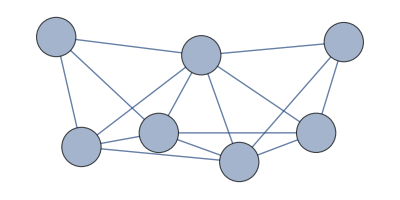

```mathematica
d=Graph[{{1,2},{1,3},{1,4},{1,6},{1,7},{2,3},{2,4},{2,5},{2,6},{3,4},{3,7},{4,5},{4,6},{4,7},{5,6}},VertexLabels-> Placed[Automatic,Center],VertexSize-> 0.5]
```

```mathematica
k=4;

vert=VertexList[d];
absvert=Length[vert];

edge=EdgeList[d];
edge=List @@@%;
absedge=Length[edge];

vertpoly={};
For[i=1,i≤absvert,i++,AppendTo[vertpoly,Indexed[x,i]^k-1]]

vars=Variables[vertpoly];

edgepoly={};
For[i=1,i≤absedge,i++,AppendTo[edgepoly,Part[PolynomialReduce[Indexed[x,Part[Part[edge,i],1]]^k-Indexed[x,Part[Part[edge,i],2]]^k,Indexed[x,Part[Part[edge,i],1]]-Indexed[x,Part[Part[edge,i],2]],{Indexed[x,Part[Part[edge,i],1]],Indexed[x,Part[Part[edge,i],2]]}],1]]];
edgepoly=Flatten[edgepoly];

graphpolyd=Join[vertpoly,edgepoly];

{test2,testgrob2}=AbsoluteTiming[GroebnerBasis[graphpolyd,vars,MonomialOrder->DegreeReverseLexicographic]]
```

{0.0539245,{x4+x5+x6+x7,x3-x6,x2-x7,x1-x5,x5^2+x5 x6+x6^2+x5 x7+x6 x7+x7^2,x6^3+x6^2 x7+x6 x7^2+x7^3,-1+x7^4}}

```mathematica
{time3,grob3}=AbsoluteTiming[ImpGrob[graphpolyd,DegreeReverseLexicographic]]
```

{2428.72,{-1+x1^4,-1+x2^4,-1+x3^4,-1+x4^4,142,(12423750697430642894506719075020013078778558541998151644282405848421944419127094155065334276778179503606059601651248556108654377191175927169892445278499023207660674625439857874325565340091819248799362564416379763710663232445531 (x4+x5+x6+x7))/173453923507897387382252395580526902270051964826337869617428611442953832846536551467767524375642075803341849646831294237261254891371371370303262903525584005826186765978334349708581189760493253837394188453247640501569992914052,(175688045234251360467755663215481990338922021030201333 (1+x6^3 x7+x6^2 x7^2+x6 x7^3))/13504432704368328186844521165965439664548562312800,-((601970121331186281867360475463503 x6^3)/14030777989902610502843664608790)-(601970121331186281867360475463503 x6^2 x7)/14030777989902610502843664608790-(601970121331186281867360475463503 x6 x7^2)/14030777989902610502843664608790-(601970121331186281867360475463503 x7^3)/14030777989902610502843664608790}}
 |  |  |  |

```mathematica
Length[grob3]
```

149

```mathematica
MonomialReduce[grob3,DegreeReverseLexicographic]
```

{-1+x7^4,x1+x2+x3+x4,x5^2+(3016041586218168473897757852325914593 x2 x6)/180575665585655947341553064155460700+(958565508524230086957782592539720669 x3 x6)/180575665585655947341553064155460700+(3857080438306919954104090536601289 x4 x6)/3009594426427599122359217735924345+(6866674864734519076463308272525634 x5 x6)/3009594426427599122359217735924345-(546565016640158942369984096188182629 x6^2)/180575665585655947341553064155460700+(556076398685263273412261946864706609 x2 x7)/180575665585655947341553064155460700-(1519248211068870160436029252953228023 x3 x7)/60191888528551982447184354718486900-(544968134379175125613836652901941 x4 x7)/601918885285519824471843547184869+(56950750906344698858006894282928 x5 x7)/601918885285519824471843547184869+(447553274639690153578494351753681304 x6 x7)/45143916396413986835388266038865175-(538991173413359863754859878579828209 x7^2)/180575665585655947341553064155460700,x2-(353300249210271205308492157529880279223425398372889724051953231991079812128811219348917575589849424471298046446560657748830462942742689745828816961737503380121367853501125707732293611779854903241371718091606563415131130 x3)/105642738683501173380801544053927212660727629364889258498225115184457715619703806471396899157678093482202219748886404689548770309135664078896150988760522787735301278718636918153515928799979995541291474576349862062937403+(75873900250536399501047020571822227328932357031414626329994674950642892879360712281800552394489632586295458914904518689752908586186124221527092337570778079845305750175413352652230834219309212749938375793031620396200 x4)/105642738683501173380801544053927212660727629364889258498225115184457715619703806471396899157678093482202219748886404689548770309135664078896150988760522787735301278718636918153515928799979995541291474576349862062937403+(75873900250536399501047020571822227328932357031414626329994674950642892879360712281800552394489632586295458914904518689752908586186124221527092337570778079845305750175413352652230834219309212749938375793031620396200 x5)/105642738683501173380801544053927212660727629364889258498225115184457715619703806471396899157678093482202219748886404689548770309135664078896150988760522787735301278718636918153515928799979995541291474576349862062937403+(353376123110521741707993204550452101450754330729921138678283226666030455021690580061199376142243914103884341905475562267520215851328875870050344054075074158201213159251301121084945842614074212454121656467399595035527330 x6)/105642738683501173380801544053927212660727629364889258498225115184457715619703806471396899157678093482202219748886404689548770309135664078896150988760522787735301278718636918153515928799979995541291474576349862062937403-(105566864783250636981300497033355390433398697007857843871895120509507072726824445759115098605283603849615924289971500170859017400549477954674623896422952009655455972968461504800863697965760686328541536200556830442541203 x7)/105642738683501173380801544053927212660727629364889258498225115184457715619703806471396899157678093482202219748886404689548770309135664078896150988760522787735301278718636918153515928799979995541291474576349862062937403,x3+(276566391869196086310657357990810176704959587304113337927710941488698023354468446180849058877763099650504415942675326604528370702529754100971705948519873200639612364132372267994654249624328175144830374355192785078192319217 x4)/43363480876974346845563098895131725567512991206584467404357152860738458211634137866941881093910518950835462411707823559315313722842842842575815725881396001456546691494583587427145297440123313459348547113311910125392498228513+(276566391869196086310657357990810176704959587304113337927710941488698023354468446180849058877763099650504415942675326604528370702529754100971705948519873200639612364132372267994654249624328175144830374355192785078192319217 x5)/43363480876974346845563098895131725567512991206584467404357152860738458211634137866941881093910518950835462411707823559315313722842842842575815725881396001456546691494583587427145297440123313459348547113311910125392498228513-(43086914485105150759252441537140915390808031619280354066429441919249760188279669420761032035032755851184957995765148232710785352140313088474844019932876128255907079130451215159150643190498985284203716738956717340314305909296 x6)/43363480876974346845563098895131725567512991206584467404357152860738458211634137866941881093910518950835462411707823559315313722842842842575815725881396001456546691494583587427145297440123313459348547113311910125392498228513+(276566391869196086310657357990810176704959587304113337927710941488698023354468446180849058877763099650504415942675326604528370702529754100971705948519873200639612364132372267994654249624328175144830374355192785078192319217 x7)/43363480876974346845563098895131725567512991206584467404357152860738458211634137866941881093910518950835462411707823559315313722842842842575815725881396001456546691494583587427145297440123313459348547113311910125392498228513,x4+x5+x6+x7,x6^3+x6^2 x7+x6 x7^2+x7^3}

```mathematica
Length[MonomialReduce[grob3,DegreeReverseLexicographic]]
```

7

```mathematica
{time4,grob4}=AbsoluteTiming[ImpGrob[graphpolyd,Lexicographic]]
```

$Aborted